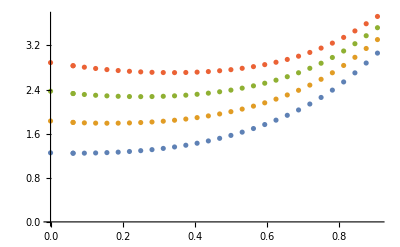

```mathematica
a={{0,1.252321},{0.062500,1.245597},{0.062500,1.245597},{0.093750,1.246588},{0.125000,1.250118},{0.156250,1.256205},{0.187500,1.264989},{0.218750,1.276692},{0.250000,1.291590},{0.281250,1.310008},{0.312500,1.332305},{0.343750,1.358866},{0.375000,1.390086},{0.406250,1.426350},{0.437500,1.467992},{0.468750,1.515268},{0.500000,1.568362},{0.531250,1.627478},{0.562500,1.692941},{0.593750,1.765216},{0.625000,1.844909},{0.656250,1.932789},{0.687500,2.029835},{0.718750,2.137265},{0.750000,2.256569},{0.781250,2.389476},{0.812500,2.537751},{0.843750,2.702379},{0.875000,2.880784},{0.906250,3.060596}};
a2={{0,1.829433},{0.062500,1.803948},{0.062500,1.803948},{0.093750,1.796028},{0.125000,1.791247},{0.156250,1.789408},{0.187500,1.790462},{0.218750,1.794465},{0.250000,1.801546},{0.281250,1.811891},{0.312500,1.825732},{0.343750,1.843331},{0.375000,1.864983},{0.406250,1.891001},{0.437500,1.921718},{0.468750,1.957483},{0.500000,1.998668},{0.531250,2.045670},{0.562500,2.098931},{0.593750,2.158950},{0.625000,2.226318},{0.656250,2.301736},{0.687500,2.386066},{0.718750,2.480357},{0.750000,2.585886},{0.781250,2.704134},{0.812500,2.836621},{0.843750,2.984210},{0.875000,3.144690},{0.906250,3.305645}};
a3={{0,2.369444},{0.062500,2.327502},{0.062500,2.327502},{0.093750,2.310152},{0.125000,2.296151},{0.156250,2.285331},{0.187500,2.277569},{0.218750,2.272829},{0.250000,2.271151},{0.281250,2.272636},{0.312500,2.277439},{0.343750,2.285756},{0.375000,2.297826},{0.406250,2.313921},{0.437500,2.334349},{0.468750,2.359451},{0.500000,2.389605},{0.531250,2.425226},{0.562500,2.466783},{0.593750,2.514800},{0.625000,2.569883},{0.656250,2.632737},{0.687500,2.704199},{0.718750,2.785268},{0.750000,2.877133},{0.781250,2.981166},{0.812500,3.098778},{0.843750,3.230826},{0.875000,3.375498},{0.906250,3.521128}};
a4={{0,2.887880},{0.062500,2.831569},{0.062500,2.831569},{0.093750,2.805032},{0.125000,2.781687},{0.156250,2.761600},{0.187500,2.744663},{0.218750,2.730804},{0.250000,2.720015},{0.281250,2.712347},{0.312500,2.707900},{0.343750,2.706825},{0.375000,2.709317},{0.406250,2.715610},{0.437500,2.725981},{0.468750,2.740747},{0.500000,2.760269},{0.531250,2.784953},{0.562500,2.815263},{0.593750,2.851722},{0.625000,2.894937},{0.656250,2.945609},{0.687500,3.004564},{0.718750,3.072779},{0.750000,3.151406},{0.781250,3.241771},{0.812500,3.345251},{0.843750,3.462762},{0.875000,3.592893},{0.906250,3.725031}};
ListPlot[{a,a2,a3,a4}]
```

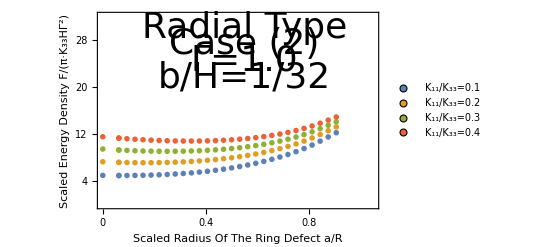

```mathematica
aa=a*Table[{1,4},{i,0,29}];
aa2=a2*Table[{1,4},{i,0,29}];
aa3=a3*Table[{1,4},{i,0,29}];
aa4=a4*Table[{1,4},{i,0,29}];
ListPlot[{aa,aa2,aa3,aa4},PlotStyle->PointSize[0.01], Frame->{True, True, True, True}, FrameTicks->{{{4,12,20,28,36},None},{{0,0.2, 0.4, 0.6, 0.8,1},None}}, PlotRange->{{0,1.05},{0,32}},FrameLabel->{{"Scaled Energy Density F/(π·K_33HΓ^2)", None},{"Scaled Radius Of The Ring Defect a/R", None}},FrameTicksStyle->Directive[Black,36],FrameStyle->Thickness[0.005],LabelStyle->Directive[Black,36],PlotLegends->Placed[PointLegend[{"K_11/K_33=0.1","K_11/K_33=0.2","K_11/K_33=0.3","K_11/K_33=0.4"},LegendMarkers->{{Graphics[Disk[]],12},{Graphics[Disk[]],12},{Graphics[Disk[]],12},{Graphics[Disk[]],12}}],{Left, Top}],Epilog->{Text[Style["Radial Type",Directive[Black,36]],{0.55,30}],Text[Style["Case (2)",Directive[Black,36]],{0.55,27.2}],Text[Style["Γ=1.0",Directive[Black,36]],{0.55,24.4}],Text[Style["b/H=1/32",Directive[Black,36]],{0.55,21.6}]}]
```